```mathematica
(*Replace your Lean executable here*)
```

```mathematica
LeanExecutable=FileNameJoin[{$HomeDirectory,".elan/bin/lean"}]
```

```mathematica
(*Set the working directory to be mm_lean/src/*)
```

```mathematica
SetDirectory["~/proj/lean/mm-lean/src"]
```

```mathematica
<<"main.m";
```

```mathematica
Lean=LeanMode[]
```

ProcessObject[…]

```mathematica
ProcessStatus[Lean]
```

Running

```mathematica
GetLeanProof[Lean,"nat.prime.dvd_of_dvd_pow"]
```

Goal | ∀ {p m n : ℕ}, nat.prime p → p ∣ m ^ n → p ∣ m
ID | 24
Rule | ∀I
Proofs |

```mathematica
GetLeanProof[Lean,"nat.prime.not_coprime_iff_dvd"]
```

Goal | ∀ {m n : ℕ}, ¬m.coprime n ↔ ∃ (p : ℕ), nat.prime p ∧ p ∣ m ∧ p ∣ n
ID | 28
Rule | ∀I
Proofs |

```mathematica
GetLeanProof[Lean,"nat.exists_infinite_primes"]
```

Goal | ∀ (n : ℕ), ∃ (p : ℕ), n ≤ p ∧ nat.prime p
ID | 31
Rule | ∀I
Proofs |

```mathematica
GetLeanInfo[Lean, "nat.min_fac"]
```

Category | Definition
Type | ℕ → ℕ
Description |

```mathematica
GetLeanInfo[Lean, "nat.exists_infinite_primes"]
```

Category | Theorem
Type | ∀ (n : ℕ), ∃ (p : ℕ), n ≤ p ∧ nat.prime p
Description |

```mathematica
GetLeanProof[Lean,"Set.singleton_inj"]
```

Goal | ∀ {x y : Set}, {x} = {y} → x = y
ID | 14
Rule | ∀I
Proofs |

```mathematica
GetLeanProof[Lean,"Set.regularity"]
```

Goal | ∀ (x : Set), x ≠ ∅ → (∃ (y : Set) (H : y ∈ x), x ∩ y = ∅)
ID | 42
Rule | ∀I
Proofs |

```mathematica
ProveUsingLeanTactic[Lean,ForAllTyped[{p,q,r},Prop,Implies[Implies[p,Implies[q,r]],Implies[And[p,q],r]]],"mm_prover", True]
```

Goal | ∀ (p q r : Prop), (p → q → r) → p ∧ q → r
ID | 12
Rule | ∀I
Proofs |

```mathematica
RunLeanTactic[Lean,ForAllTyped[{p,q,r},Prop,Implies[Implies[p,Implies[q,r]],Implies[And[p,q],r]]],"print_translation",True]
```

Lean native | ∀ (p q r : Prop), (p → q → r) → p ∧ q → r
Mathematica form |

```mathematica
<<"../_target/deps/mathematica/src/lean_form.m"
```

```mathematica
<<"natural_deduction_graphs.wl"
```

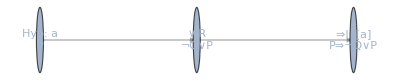

```mathematica
DiagramOfFormula[Lean,ForAll[{P,Q},Implies[P,Or[Not[Q],P]]],{P,Q}]
```

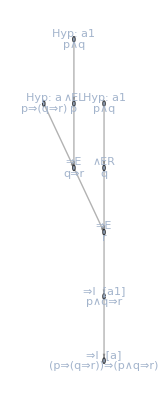

```mathematica
DiagramOfFormula[Lean,ForAllTyped[{p,q,r},Prop,Implies[Implies[p,Implies[q,r]],Implies[And[p,q],r]]],{p,q,r}]
```

```mathematica
RunLeanTactic[Lean,ForAllTyped[{s,t},set[nat],SetInter[s,SetUnion[t,SetCompl[s]]]==SetInter[s,t]],"normalize_set_lemmas"]
```

set_distrib_right : ∀ {α : Type ?} (s t u : set α), s ∩ (t ∪ u) = s ∩ t ∪ s ∩ u
set.union_empty : ∀ {α : Type ?} (a : set α), a ∪ ∅ = a
nonempty_of_inhabited : ∀ {α : Sort ?} [_inst_1 : inhabited α], nonempty α
set.inter_compl_self : ∀ {α : Type ?} (s : set α), s ∩ sᶜ = ∅

```mathematica
ProveUsingLeanTactic[Lean,ForAllTyped[{s,t},set[nat],SetInter[s,SetUnion[t,SetCompl[s]]]==SetInter[s,t]],"simp", True]
```

Goal | ∀ (s t : set ℕ), s ∩ (t ∪ sᶜ) = s ∩ t
ID | 56
Rule | eq.mpr
Proofs |

```mathematica
QuitLeanMode[Lean]
```